```mathematica
Clear["Global`*"];
```

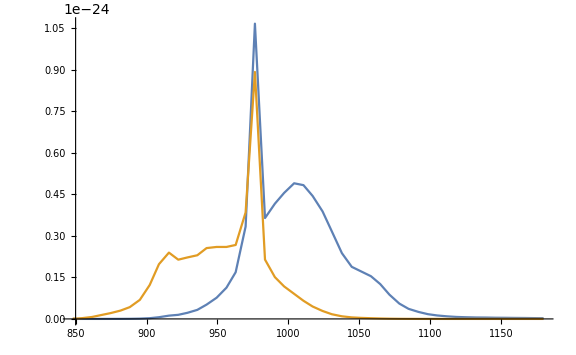

```mathematica
Data=Import["CrossSection.xls", Path->NotebookDirectory[]][[1,5;;,{4,15,16}]];
σe := Interpolation[Data[[All,{1,2}]], InterpolationOrder->1];
σa := Interpolation[Data[[All,{1,3}]], InterpolationOrder->1];
Plot[{σe[λ],σa[λ]},{λ, Data[[1,1]], Data[[-1,1]]},PlotRange->All, ImageSize->Large]
```

```mathematica
c = 3×10^8; (* м/c *)
τ=1.45×10^-3; (* c *)
NN = 300; (* ppm *)
NN = 6.62×10^22NN; (* м^-3 *)
h = 6.63×10^-34; (* Постоянная планка *)
Aeff = Pi/4 7^2×10^-12;
(* эффективная площадь моды *)
λp = 960; (* нм *)
λs = 1064; (* нм *)
Ps = Aeff h c / (λs 10^-9);
Pp = Aeff h c / (λp 10^-9);
L = 2; (* длина усилителя *)
```

```mathematica
equation1 = (-σe[λs] N2[z]  + σa[λs] N1[z]) ρs[z] + (-σe[λp] N2[z]  + σa[λp] N1[z]) ρp[z] -  N2[z]/τ == 0;
equation2 = D[ρs[z], {z,1}]==(σe[λs] N2[z]  - σa[λs] N1[z]) ρs[z];
equation3 = D[ρp[z], {z,1}]==(σe[λp] N2[z]  - σa[λp] N1[z]) ρp[z];
equation4 = N1[z] + N2[z] == NN;
equations = {equation1, equation2,equation3,equation4};
startingEquation1 = ρp[0] == 0.5/Pp;
startingEquation2 = ρs[0] == 0.01/Pp;
startingEquations = {startingEquation1,startingEquation2};
```

```mathematica
solution = NDSolve[{equations, startingEquations},{ρs[z], ρp[z], N1[z], N2[z]}, {z,0,L}, AccuracyGoal->Infinity, PrecisionGoal->Automatic];
```

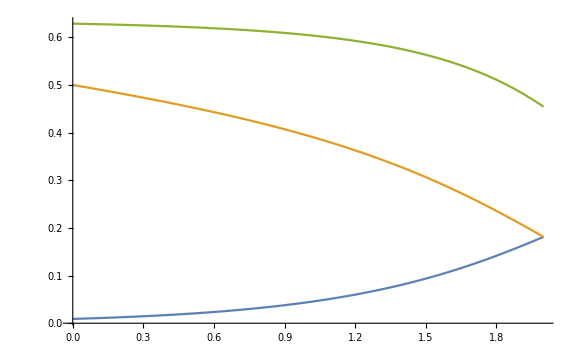

```mathematica
Plot[Evaluate[{ρs[z]Ps, ρp[z]Pp, N2[z]/NN}/.solution],{z,0,L}, PlotRange->All, ImageSize->Large]
```